```mathematica
readData[validDataPath_]:=Module[{fpath=validDataPath},Association[Import[fpath,"JSON"]]];
extractData[experiment_]:=Module[{expmt=experiment},{expmt["domain"],DeleteDuplicates[Map[Association,expmt["population"]]]}]
reportPopulation[population_]:=Module[{pop=population},
census=Length[pop];
scores=Map[#["score"]&, pop];
sum=Fold[Plus, 0, scores];
max=Max[scores];
min=Min[scores];
Print[StringTemplate["`a` unique pop members with:"][<|"a"->census|>]];
Print[StringTemplate["  max `a`"][<|"a"->max|>]];
Print[StringTemplate["  avg `a`"][<|"a"->sum/census|>]];
Print[StringTemplate["  ctr `a`"][<|"a"->(min+max)/2|>]];
Print[StringTemplate["  min `a`"][<|"a"->min|>]]
]
plotBestRoute[cityPositions_,population_]:=Module[{cities=cityPositions, pop=population},
ListLinePlot[Map[cities[[#+1]]&,First[pop]["route"]], AspectRatio->1]
]
travSalesPlot[validDataPath_]:=Module[{fname=validDataPath},
x=readData[fname];
{cityXYs,pops}=extractData[x];
plotBestRoute[cityXYs,pops]
]
```

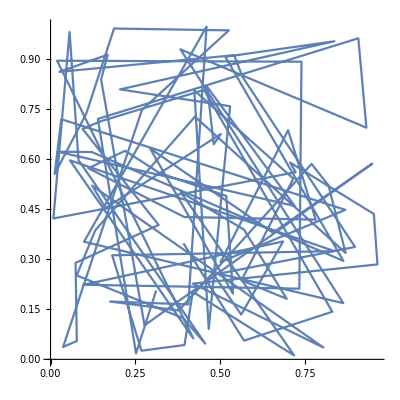

```mathematica
travSalesPlot["~/projects/elixir/gelid/gelid/data/20230217182025Z-1.json"]
```

```mathematica
readData["~/projects/elixir/gelid/gelid/data/20230217182025Z-1.json"];
{cityPositions,population}=extractData[%];
cityPositions;
population;
plotBestRoute[cityPositions,population]
```

-Graphics-